## Definitions

```mathematica
KP[r__]:=KroneckerProduct[r]
```

```mathematica
Needs["QDENSITY`Qdensity`"];
Needs["QDENSITY`QCWave`"];
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

### General function definitions

```mathematica
Stokesfromρ[ρ_]:=Table[Tr[Subscript[σ, i].ρ],{i,1,3}]
Stokesfromψ[ψ_]:=Stokesfromρ[ρfromψ[ψ]]
Fidfromρ[ρ_,σ_]:=Re[Tr[MatrixPower[MatrixPower[ρ,0.5].σ.MatrixPower[ρ,0.5],0.5]]^2]
```

```mathematica
?QDENSITY`Qdensity`*
```

### My extra definitions

Useful functions for easily constructing multi-qubit matrices - lets you specify any two qubit matrix, as opposed to only Pauli matrices

```mathematica
Zero2b2T[L_]:=Table[IdentityMatrix[2],{L}]
```

```mathematica
OneOpArb[L_, q1_, op1_] := SPArb[L, ReplacePart[Zero2b2T[L], op1, q1]];
```

```mathematica
TwoOpArb[L_,q1_,q2_,op1_,op2_]:=SPArb[L,ReplacePart[ReplacePart[Zero2b2T[L],op1,q1],op2,q2]];
```

```mathematica
SPArb[L_, Q_] := SP[L, Q] = If [L > 1, TensorProductQ[{SPArb[L - 1,Drop[Q,-1]],Q[[L]]}],Q[[1]]];
```

E.g. To show it works, quickly make a CNOT between qubits 1 and 3

```mathematica
CNOT[3,1,3]==TwoOpArb[3,1,3,Subscript[𝒫, 0],Subscript[σ, 0]]+TwoOpArb[3,1,3,Subscript[𝒫, 1],Subscript[σ, 1]]
```

True

### Single qubit gates

```mathematica
(*Definition of single spin rotations using the qdensity package
Nomenclature:  r followed by a capital letter --> rotation by π around the axis specified by the letter.
			r followed by a lower case letter: rotation by π/2 around the axis specified by that letter
The rotation direction is given by the appended letter m or p*)

{rxp,rXp,ryp,rYp,rzp,rZp}=Table[AF[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[AF[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
```

## Cracking on

```mathematica
ρ={{p00,c0001,c0010,c0011},{c0001*,p01,c0110,c0111},{c0010*,c0110*,p10,c1011},{c0011*,c0111*,c1011*,p11}}
```

(p00 | c0001 | c0010 | c0011
Conjugate[c0001] | p01 | c0110 | c0111
Conjugate[c0010] | Conjugate[c0110] | p10 | c1011
Conjugate[c0011] | Conjugate[c0111] | Conjugate[c1011] | p11)

```mathematica
ZZ = Diagonal[ρ];
XX=Diagonal[#1.#2.#1†&[TensorProductQ[{rym,rym}],ρ]];
YY=Diagonal[#1.#2.#1†&[TensorProductQ[{rxp,rxp}],ρ]];
```

```mathematica
XX={1/4(1+2 (Re[c0001]+Re[c0010]+Re[c0011]+Re[c0110]+Re[c0111]+Re[c1011])),1/4(1+2 (-Re[c0001]+Re[c0010]-Re[c0011]-Re[c0110]+Re[c0111]-Re[c1011])),1/4(1+2 (Re[c0001]-Re[c0010]-Re[c0011]-Re[c0110]-Re[c0111]+Re[c1011])),1/4(1+2 (-Re[c0001]-Re[c0010]+Re[c0011]+Re[c0110]-Re[c0111]-Re[c1011]))}

YY={1/4(1+2 (-Im[c0001]-Im[c0010]-Re[c0011]+Re[c0110]-Im[c0111]-Im[c1011])),1/4(1+2 (Im[c0001]-Im[c0010]+Re[c0011]-Re[c0110]-Im[c0111]+Im[c1011])),1/4(1+2 (-Im[c0001]+Im[c0010]+Re[c0011]-Re[c0110]+Im[c0111]-Im[c1011])),1/4(1+2 (+Im[c0001]+Im[c0010]-Re[c0011]+Re[c0110]+Im[c0111]+Im[c1011]))}
```

(1/4 (1+2 (Re[c0001]+Re[c0010]+Re[c0011]+Re[c0110]+Re[c0111]+Re[c1011]))
1/4 (1+2 (-Re[c0001]+Re[c0010]-Re[c0011]-Re[c0110]+Re[c0111]-Re[c1011]))
1/4 (1+2 (Re[c0001]-Re[c0010]-Re[c0011]-Re[c0110]-Re[c0111]+Re[c1011]))
1/4 (1+2 (-Re[c0001]-Re[c0010]+Re[c0011]+Re[c0110]-Re[c0111]-Re[c1011])))

(1/4 (1+2 (-Im[c0001]-Im[c0010]-Im[c0111]-Im[c1011]-Re[c0011]+Re[c0110]))
1/4 (1+2 (Im[c0001]-Im[c0010]-Im[c0111]+Im[c1011]+Re[c0011]-Re[c0110]))
1/4 (1+2 (-Im[c0001]+Im[c0010]+Im[c0111]-Im[c1011]+Re[c0011]-Re[c0110]))
1/4 (1+2 (Im[c0001]+Im[c0010]+Im[c0111]+Im[c1011]-Re[c0011]+Re[c0110])))

```mathematica
XX/.{c0001->0,c0010->0,c1011->0,c0111->0}
YY/.{c0001->0,c0010->0,c1011->0,c0111->0}
```

(1/4 (1+2 (Re[c0011]+Re[c0110]))
1/4 (1+2 (-Re[c0011]-Re[c0110]))
1/4 (1+2 (-Re[c0011]-Re[c0110]))
1/4 (1+2 (Re[c0011]+Re[c0110])))

(1/4 (1+2 (-Re[c0011]+Re[c0110]))
1/4 (1+2 (Re[c0011]-Re[c0110]))
1/4 (1+2 (Re[c0011]-Re[c0110]))
1/4 (1+2 (-Re[c0011]+Re[c0110])))

Logarithmic negativity gives an upper bound to the distillable entanglement

```mathematica
ρpt=PartialTranspose[{1},ρ];
logNegativity=Log[2,FullSimplify[Total[SingularValueList[ρpt/.{c0001->0,c0010->0,c1011->0,c0111->0,c0011->0}]],Assumptions->{p00>0,p10>0,p01>0,p11>0,p00+p10+p01+p11==1,{c0110}∈Reals}]]
```

Log[p01+p10+(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))/(√2)+(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√2)]/Log[2]

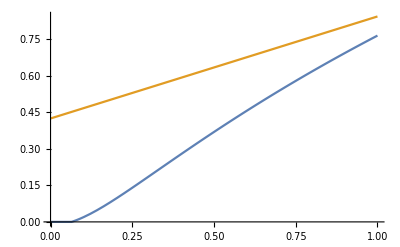

```mathematica
zz={0.005,0.495,0.355};
Fidelity [p01_,p10_,c0110_]:=1/2(p01+p10+2c0110)
Plot[Evaluate[{logNegativity,Fidelity[p10,p01,c0110]}/.{p00->zz[[1]],p01->zz[[2]],p10->zz[[3]],p11->1-Total[zz],c0110->α Sqrt[zz[[2]] zz[[3]]]}],{α,0,1}]
```

```mathematica
error=Sqrt[(Simplify[D[logNegativity,c0110]] * δc0110)^2+(Simplify[D[logNegativity,p00]] * δp00)^2+(Simplify[D[logNegativity,p01]] * δp01)^2+(Simplify[D[logNegativity,p10]] * δp10)^2+(Simplify[D[logNegativity,p11]] * δp11)^2]
```

√((2 c0110^2 ((1+(-1+p01+p10)/(√(4 c0110^2+(-1+p01+p10+2 p11)^2)))/(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))+(1+(-1+p01+p10)^2/(√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2)))))^2 δc0110^2)/((p01+p10+(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))/(√2)+(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√2))^2 Log[2]^2)+(p00^2 δp00^2)/(2 (2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))) (p01+p10+(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))/(√2)+(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√2))^2 Log[2]^2)+((8+(2 √2 (-1+p01+p10) (4 c0110^2+(-1+p01+p10) (-1+p01+p10+2 p11)+(-1+p01+p10+2 p11)^2))/(√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2)) √(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))+(4 √2 (2 c0110^2+(-1+p01+p10+p11) (-1+p01+p10+2 p11+√(4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√(4 c0110^2+(-1+p01+p10+2 p11)^2) √(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2))))^2 δp01^2)/(64 (p01+p10+(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))/(√2)+(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√2))^2 Log[2]^2)+((8+(2 √2 (-1+p01+p10) (4 c0110^2+(-1+p01+p10) (-1+p01+p10+2 p11)+(-1+p01+p10+2 p11)^2))/(√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2)) √(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))+(4 √2 (2 c0110^2+(-1+p01+p10+p11) (-1+p01+p10+2 p11+√(4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√(4 c0110^2+(-1+p01+p10+2 p11)^2) √(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2))))^2 δp10^2)/(64 (p01+p10+(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))/(√2)+(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√2))^2 Log[2]^2)+(((2 (-1+p01+p10+2 p11+((-1+p01+p10) (-1+p01+p10+2 p11))/(√(4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))+(2 (p11+((-1+p01+p10)^2 (-1+p01+p10+2 p11))/(√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2)))))/(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2)))))^2 δp11^2)/(8 (p01+p10+(√(2 c0110^2+p11^2+(-1+p01+p10+p11)^2+(-1+p01+p10) √(4 c0110^2+(-1+p01+p10+2 p11)^2)))/(√2)+(√(2 c0110^2+p00^2+p11^2+√((-1+p01+p10)^2 (4 c0110^2+(-1+p01+p10+2 p11)^2))))/(√2))^2 Log[2]^2))

```mathematica
logNegativity/.{p00->0.1,p01->0.4,p10->0.4,p11->0.1,c0110->0.3,δp00->0.01,δp01->0.01,δp10->0.01,δp11->0.01,δc0110->0.0502493781056}
error/.{p00->0.1,p01->0.4,p10->0.4,p11->0.1,c0110->0.3,δp00->0.01,δp01->0.01,δp10->0.01,δp11->0.01,δc0110->0.0502493781056}
```

0.485427

0.104869

## Shannon entropy

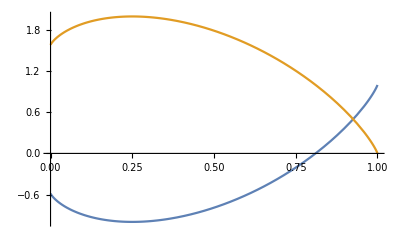

```mathematica
S[p_]:=(-p Log[2,p]-(1-p)Log[2,(1-p)/3])
Plot[{1-S[p],S[p]},{p,0,1}]
```

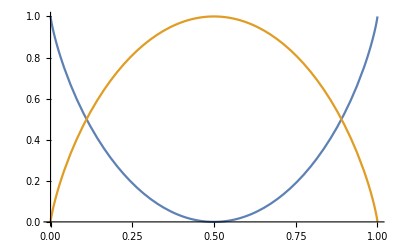

```mathematica
Sknown[p_]:=(-p Log[2,p]-(1-p)Log[2,(1-p)])
Plot[{1-Sknown[p],Sknown[p]},{p,0,1}]
```